# Въведение

```mathematica
7+8
```

15

```mathematica
vec = {6,Pi,π,{3.76,6},Tan[9.8]}
```

{6,π,π,{3.76,6},0.393883}

```mathematica
vec1 = {6.0,Pi,π,{3.76,6.},Tan[9.8]};
(* изписваме числата като десетични   *)
```

```mathematica
vec1
```

{6.,π,π,{3.76,6.},0.393883}

```mathematica
vec1
```

{6,π,π,{3.76,6},0.393883}

функциите действат върху цели списъци едновременно

```mathematica
Cos[vec]
```

{Cos[6],-1,-1,{-0.814803,Cos[6]},0.923426}

```mathematica
Cos[vec1]
```

{0.96017,-1,-1,{-0.814803,0.96017},0.923426}

пишем текстова клетка с Alt+7

# КЧМ за решаване на нелинейни уравнения

Задача: Дадено ни е уравнението:
x^4-12 x^3 +77sinx- 32 = 0
1. Да се визуализира функцията
2. Да се определи броя на корените
3. Да се локализира един от тях
4. Да се уточни локализирания корен
5. Оценка на грешката

```mathematica
f[x_]:=x^4-12 x^3 +77Sin[x]-32
```

## 1. Да се визуализира функцията

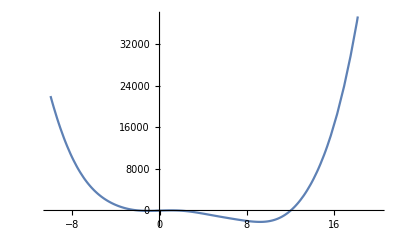

```mathematica
Plot[f[x],{x,-10,20}]
```

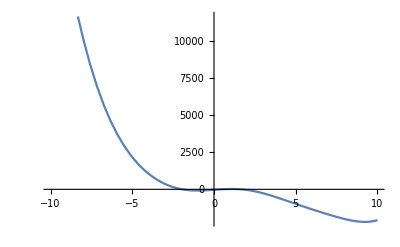

```mathematica
Plot[f[x],{x,-10,10}]
```

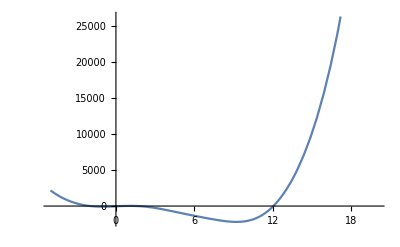

```mathematica
Plot[f[x],{x,-5,20}]
```

## 2. Да се определи броя на корените

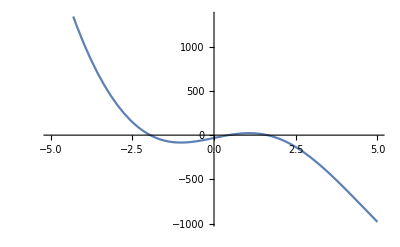

```mathematica
Plot[f[x],{x,-5,5}]
```

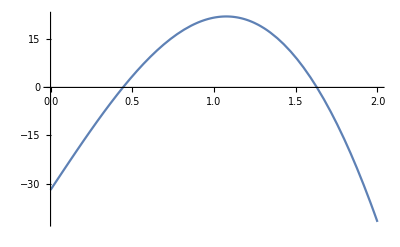

```mathematica
Plot[f[x],{x,0,2}]
```

## 3. Да се локализира един от тях

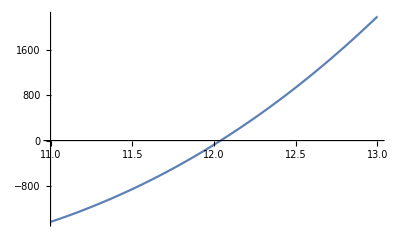

```mathematica
Plot[f[x],{x,11,13}]
```

```mathematica
f[11.]
```

-1440.

```mathematica
f[13.]
```

2197.35

Извод: 
(1) Функцията f(x) е непрекъсната, защото е сума от непрекъснати функции (полином и синус)
(2) f(11) = -1440 < 0
       f(13) = 2197.35.... > 0
       Функцията има различни знаци в двата края на разглеждания интервал [11; 13].
       Следователно от (1) и (2) следва, че в интервала [11; 13] функцията има поне един корен.

## 4. Да се уточни локализирания корен

## 5. Оценка на грешката